```mathematica
f[x_]:=1+Cos[x]
```

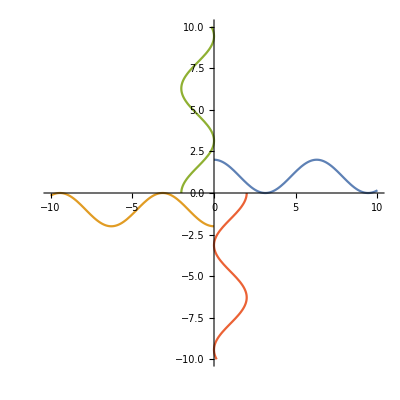

```mathematica
ParametricPlot[{{t,f[t]},{-t,-f[t]},{-f[t],t},{f[t],-t}},{t,0,10}]
```

```mathematica
x->y
y->z
z->x
```

```mathematica
Nest[f,a,0]
```

5.83203

```mathematica
interpolate[{x_,y_,z_},{x2_,y2_,z2_},n_]:={Piecewise[{{InterpolatingPolynomial[{{x,n},{x2,n+1}},t], x≠x2}, {x, x==x2}}],Piecewise[{{InterpolatingPolynomial[{{y,n},{y2,n+1}},t], y≠y2}, {y, y==y2}}],Piecewise[{{InterpolatingPolynomial[{{z,n},{z2,n+1}},t], z≠z2}, {z, z==z2}}]}
```

```mathematica
g[a_,t2_]:=((Piecewise[{{interpolate[{Nest[f,a,Floor[t2]],Nest[f,a,Floor[t2]+1],0},{0,Nest[f,a,Floor[t2]+1],Nest[f,a,Floor[t2]+2]},t], 0≤Mod[t2,3]<1}, {interpolate[{0,Nest[f,a,Floor[t2]],Nest[f,a,Floor[t2]+1]},{Nest[f,a,Floor[t2]+2],0,Nest[f,a,Floor[t2]+1]},t], 1≤Mod[t2,3]<2}, {interpolate[{Nest[f,a,Floor[t2]+1],0,Nest[f,a,Floor[t2]]},{Nest[f,a,Floor[t2]+1],Nest[f,a,Floor[t2]+2],0},t], 2≤Mod[t2,3]<3}}])/.t->t2)
```

```mathematica
g[a,1]
```

{1.56192,1.47367,0.676765}

```mathematica
a=RandomReal[{3,10}];
ParametricPlot3D[{{t,f[t],0},{0,t,f[t]},{f[t],0,t},{t+f[t],t+f[t],t+f[t]}},{t,0,10},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
FindInstance[1.000+Cos[x]==x,x,Reals]
```

{{x→1.28343}}

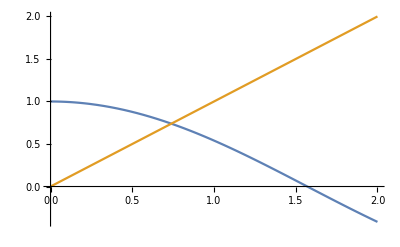

```mathematica
Plot[{Cos[x],x},{x,0,2}]
```

```mathematica
Last[CellularAutomaton[30,{{1},0},100]]
```

```mathematica
tofrac[x_]:=FromDigits[{x,0},2]
```

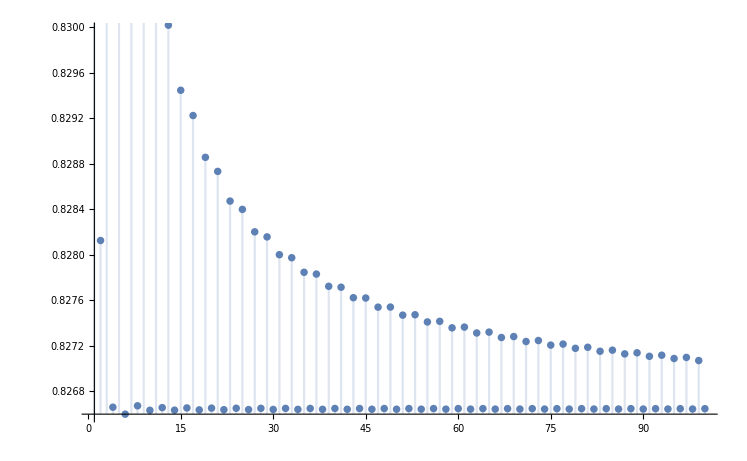

```mathematica
Monitor[DiscretePlot[Sum[tofrac[Last[CellularAutomaton[30,{{1},0},t]]],{t,1,s}]/s,{s,1,100}],{s,t}]
```

```mathematica
Monitor[Sum[tofrac[Last[CellularAutomaton[30,{{1},0},t]]],{t,1,1200}]/1200,t]
```

588193753881344686027804017016796931612311672319980372827549570656300646340629231828720290007084904341306476396676575012092541823234183357794946609892449839029352786351389661738409913078729842187821380093560867350481420979854071244430306501905834920378835575037005495979235103966893429408182239692967956882424469438083846752668308632596143659026214369291866388648562495944795730195674190895712275663510649513609464998213480519237975608087213651707700636735037051817272799898390444800809392464378668467766889166639694434643032458786730931037094350558473081694267190229961519240546392331375094130209572040631594273347105607674261201482186349822088146002132110525487161488306503191181728657996326894687586235084651426234506587853/711542483495947521889952865854134071929143438746319979558597554888538547193389505721898312485077107137691367283028410245738774303260182105641211226188751592644112460626751317772029121675655643544550151663694645929761618133470993830897052646028373338274583923103914362012261166546624111641872392710164807675277420654672601848471767728815215393456307738741273376732441941389611278167418149655624969370028349005676000884095748271578321500786251343504313026200304084658093942982058320030167176904120955449094014221055611625217037917064067386547584640311742668980213361552023149171282725920170172997951259022340960743424195901889613658026392966791645933802796999560565929701066220311728316079916643169462633623030307806534592102400

```mathematica
N[Out[450],100]
```

0.8266460085298542133811031787135176092412049482183950539746256454781629367830888677118873558584725518

```mathematica
RealDigits[0.2143]
```

{{2,1,4,3,0,0,0,0,0,0,0,0,0,0,0,0},0}

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},2000]]
```

-Graphics-

```mathematica
[g,h]==g^-1 h^-1 g h
g^h==h^-1 g h
```

```mathematica
⟨⟨a,b|o(a)=2,o(b)=4,o(ab)=11,o(z)=5,o([b,z])=1;z=abab(b^2(b^2)^abab)^5⟩⟩
```

```mathematica
rs[s_,n_]:=StringJoin[Table[s,{i,0,n}]]
rs["2",3]
```

2222

```mathematica
a^-1=A
b^-1=B
```

```mathematica
a^2
b^4
(ab)^11
z=abab(b A B A b b a b a b)^5
z^5
B z^-1 b z
```

```mathematica
slist={rs["a",2],
rs["b",4],
rs["ab",11],
StringJoin["abab",rs["bABAbbabab",5]],
rs[StringJoin["abab",rs["bABAbbabab",5]],5],
StringJoin["B",StringJoin[StringReplace[Reverse[Characters[StringJoin["abab",rs["bABAbbabab",5]]]],{"a"->"A","b"->"B","A"->"a","B"->"b"}]],"b",StringJoin["abab",rs["bABAbbabab",5]]]}
```

```mathematica
{"aaa","bbbbb","abababababababababababab","ababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbabab","ababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbabab","BBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABAbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbabab"}
```

```mathematica
StringLength["BBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABAbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababababababababababbbbbaaa"]
```

477

```mathematica
mstring="BBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABAbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababababababababababbbbbaaa"
```

```mathematica
(477(477+1))/2
```

```mathematica
114003*49*49/10^6//N
```

273.721

```mathematica
∑_(i=1)^477 ∑_(j=1)^i j
```

```mathematica
18202479*0.0008429482000000000141426426125690341
```

15343.746908587800257431155159793

```mathematica
%/(60*60)
```

4.26215191905216673817532087772027

```mathematica
FactorInteger[477]
```

{{3,2},{53,1}}

```mathematica
49*49
```

2401

```mathematica
Mod[2^477,477]
```

35

```mathematica
StringTake["abababababababababababab",{1,5}]
```

ababa

```mathematica
StringLength["makemeasandwich"]
```

15

```mathematica
substringindices[n_]:=Partition[Flatten[Table[Table[{i,i+j},{i,1,n-j}],{j,0,n-1}]],2]
substringindices[4]
```

{{1,1},{2,2},{3,3},{4,4},{1,2},{2,3},{3,4},{1,3},{2,4},{1,4}}

```mathematica
Table[Block[{test=substringindices[k]},InterpolatingPolynomial[Table[{test[[i]],i},{i,1,Length[test]}],{n,m}]],{k,3,10}]
Map[MatrixForm[CoefficientList[#,{n,m}]]&,%]
Table[((2x+1)/2-m/2) m+n,{x,3,10}]
```

{(7/2-m/2) m+n,(9/2-m/2) m+n,(11/2-m/2) m+n,(13/2-m/2) m+n,(15/2-m/2) m+n,(17/2-m/2) m+n,(19/2-m/2) m+n,(21/2-m/2) m+n}

{(0 | 7/2 | -1/2
1 | 0 | 0),(0 | 9/2 | -1/2
1 | 0 | 0),(0 | 11/2 | -1/2
1 | 0 | 0),(0 | 13/2 | -1/2
1 | 0 | 0),(0 | 15/2 | -1/2
1 | 0 | 0),(0 | 17/2 | -1/2
1 | 0 | 0),(0 | 19/2 | -1/2
1 | 0 | 0),(0 | 21/2 | -1/2
1 | 0 | 0)}

{(7/2-m/2) m+n,(9/2-m/2) m+n,(11/2-m/2) m+n,(13/2-m/2) m+n,(15/2-m/2) m+n,(17/2-m/2) m+n,(19/2-m/2) m+n,(21/2-m/2) m+n}

```mathematica
(*converts (x,y) pair to position in list for string length n*)
(* n > 2 *)
(*block added to work with totriangularpair instead of the "raw" indices used to find the function*)
pairtoindex[{x_,y0_},n_]:=Module[{y=y0-x},((2n+1)/2-y/2) y+x]
```

```mathematica
∑_(i=a)^b i
```

-1/2 (-1+a-b) (a+b)

```mathematica
Solve[-1/2 (-1+a-b) (a+b)==c&&a>0&&b>0&&b(b+1)/2≥c>b>a,a,Reals]
```

{{a→ConditionalExpression[1/2+1/2 √(1+4 b+4 b^2-8 c),b>1&&b<c<1/2 (b+b^2)]}}

```mathematica
(*replacing b with l for string length for clarity *)
```

```mathematica
totriangularpair[n_,l_]:={#[[1]],#[[1]]+#[[2]]}&@Module[{a=Floor[1/2+1/2 √(1+4 l+4 l^2-8 n)]+1},{n-(-1/2 (-1+a-l) (a+l)),l-(a-1)}]
Table[totriangularpair[n,4],{n,1,10}]
Map[pairtoindex[#,4]&,%]
```

{{1,1},{2,2},{3,3},{4,4},{1,2},{2,3},{3,4},{1,3},{2,4},{1,4}}

{1,2,3,4,5,6,7,8,9,10}

```mathematica
nthsubstring[string_,n_]:=StringTake[string,totriangularpair[n,StringLength[string]]]
```

```mathematica
Table[nthsubstring["MAKE",n],{n,1,10}]
```

{M,A,K,E,MA,AK,KE,MAK,AKE,MAKE}

```mathematica
(* want to input matrix a, matrix b, and string of {a,b,A,B} to get matrix product where aA==bB==e *)
```

```mathematica
modoutmatrix[mat_,mod_]:=Map[Mod[#,mod]&,mat,{2}]
```

```mathematica
stringtomat[ mata_, matb_, string_,mod_]:=
Module[{a=mata,b=matb,A=mInverse[mata,mod],B=mInverse[matb,mod]},Fold[modoutmatrix[#1.(Piecewise[{{a, StringTake[string,{#2}]=="a"}, {b, StringTake[string,{#2}]=="b"}, {A, StringTake[string,{#2}]=="A"}, {B, StringTake[string,{#2}]=="B"}}]),mod]&,IdentityMatrix[Length[mata]],Range[StringLength[string]]]]
stringtomat[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),"ababBABA",2]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
modoutmatrix[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}).({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}).({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}).({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),2]
```

{{0,1,0},{1,1,0},{0,0,1}}

```mathematica
randomSymMat=Module[{mat=RandomInteger[1,{#,#}],upper,diag},upper=UpperTriangularize[mat,1];
diag=DiagonalMatrix[Diagonal@mat];
diag+upper+Transpose[upper]]&;
First[AbsoluteTiming[testmat=randomSymMat[10000]]]
```

9.601026

```mathematica
testmathalf=Table[Table[testmat[[i,j]],{i,1,j}],{j,1,Length[testmat]}];
```

```mathematica
makesymmetric[mat_]:=(Print["making symmetric..."];Block[{paddedmat=Map[PadRight[#,Length[mat]]&,mat]},Block[{mirroredmat=paddedmat+Transpose[paddedmat]},Map[Piecewise[{{1, #>0}, {0, #≥0}}]&,mirroredmat,{2}]]])
```

```mathematica
AbsoluteTiming[makesymmetric[testmathalf]==testmat]
```

making symmetric...

{28.78451,True}

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x≠True}}]
numofsubstrings[string_]:=StringLength[string](StringLength[string]+1)/2
```

```mathematica
substringgraph[mata_,matb_,string_,mod_]:=
makesymmetric[ParallelTable[Table[
(tf[stringtomat[ mata, matb,nthsubstring[string,z],mod]==stringtomat[ mata, matb,nthsubstring[string,w],mod]]),{z,1,w}],{w,1,numofsubstrings[string]}]]
AbsoluteTiming[stringtomat[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),"ababBABA",2]//MatrixForm]
AbsoluteTiming[substringgraph[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),"ababBABA",2]//MatrixForm]
```

{0.00043,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

making symmetric...

{1.1712,(1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1)}

```mathematica
ArrayPlot[substringgraph[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),"ababBABA",2]]
```

-Graphics-

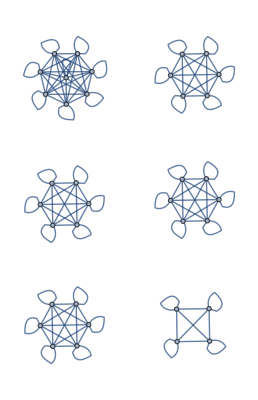

```mathematica
AdjacencyGraph[substringgraph[({{1, 1, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),"ababBABA",2]]
```

```mathematica
0.14024200000000000554400969576818170026/(36*36)
```

0.0001082114197530864240308716788334735342

```mathematica
(*Subscript[S, 4](3)
a^2=b^5=(ab)^9=[a,b]^3=[a,bab]^2*)
"aa","bbbbb","ababababababababab","ABabABabABab","ABABababABABabab"
```

```mathematica
"ABabABabABabABABababABABabababababababababbbbbaa"
```

```mathematica
Partition[{0,1,0,0,1,0,0,0,3,3,1,0,1,1,0,1},4]
%//MatrixForm
Partition[{0,0,1,0,0,0,0,1,1,0,0,1,0,1,1,1},4]
%//MatrixForm
```

{{0,1,0,0},{1,0,0,0},{3,3,1,0},{1,1,0,1}}

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
3 | 3 | 1 | 0
1 | 1 | 0 | 1)

{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,1}}

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 1)

```mathematica
AbsoluteTiming[stringtomat[{{0,1,0,0},{1,0,0,0},{3,3,1,0},{1,1,0,1}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,1}},"ABabABabABabABABababABABabababababababababbbbbaa",4]]
```

{0.00285,{{2,2,3,1},{1,2,1,2},{3,3,2,1},{1,1,0,2}}}

```mathematica
{0.00148200000000000002738087534481792318`3.1914481169229334,{{2,2,3,1},{1,2,1,2},{3,3,2,1},{1,1,0,2}}}
```

```mathematica
s43graphmatwithtiming=AbsoluteTiming[substringgraph[{{0,1,0,0},{1,0,0,0},{3,3,1,0},{1,1,0,1}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,1}},"ABabABabABabABABababABABabababababababababbbbbaa",4]];
```

making symmetric...

```mathematica
{First[s43graphmatwithtiming],First[s43graphmatwithtiming]/18424}
```

{512.04679,0.027792379}

```mathematica
s43graphmat=Last[s43graphmatwithtiming];
```

```mathematica
Export["s43graphmat.txt",InputForm[s43graphmat]]
```

s43graphmat.txt

```mathematica
ArrayPlot[s43graphmat]
```

-Graphics-

```mathematica
AdjacencyGraph[s43graphmat]
```

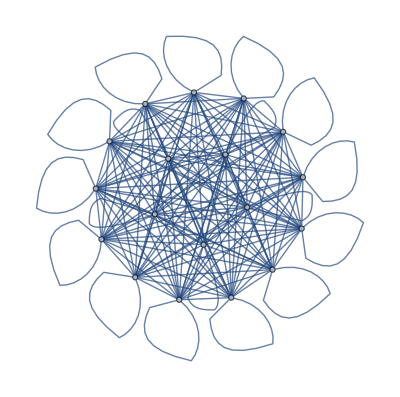
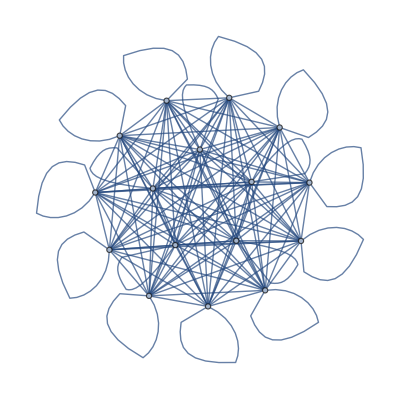
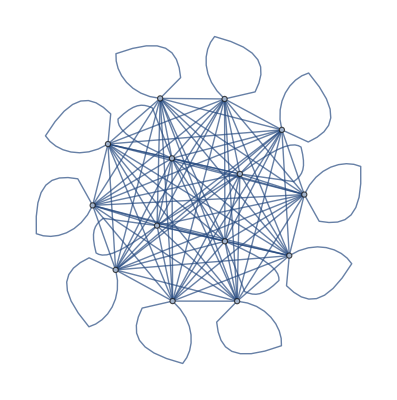
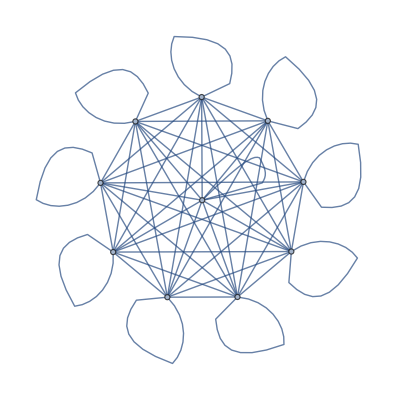
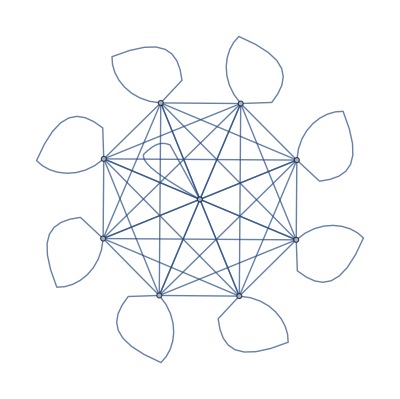
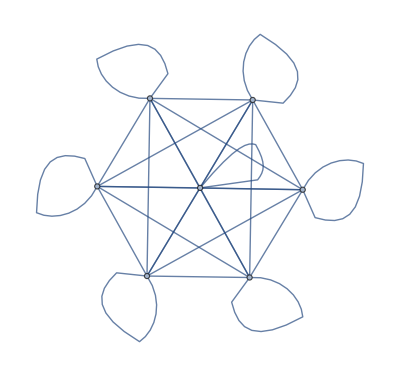
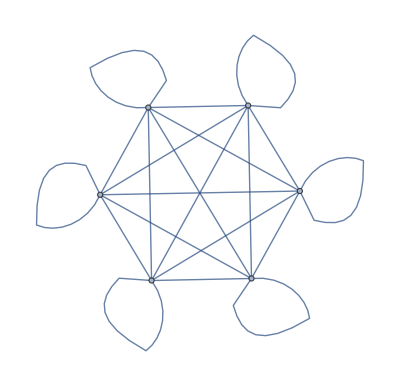
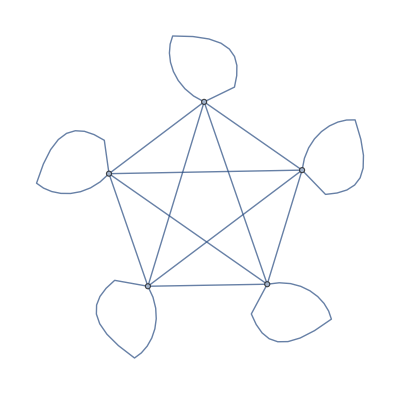

```mathematica
DeleteDuplicates[Subgraph[%,#]&/@ConnectedComponents[%],IsomorphicGraphQ[#1,#2]==True&]
```

```mathematica
AbsoluteTiming[stringtomat[{{0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,5,2,4,3,4,2,5,2,2,0,6,1,3,4,5,0,3,3,0,3,1,0,0,2,2,5,3,2,5,3,6,4,6,4,0,2,5,6,4,6,4,5,5,6},{6,2,5,2,4,6,1,1,4,1,1,2,3,2,6,6,2,0,1,5,1,6,0,3,2,6,4,2,2,4,0,0,2,0,1,3,1,1,5,4,4,5,1,3,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,5,2,3,0,1,5,5,3,4,1,4,6,3,2,3,5,2,5,3,4,2,1,3,6,3,0,4,4,1,4,5,1,4,6,2,2,6,3,1,5,1,0,6,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,1,4,4,1,2,6,0,4,3,1,6,5,4,1,1,0,6,1,1,4,3,5,5,6,1,6,4,3,1,0,6,2,5,1,5,3,4,4,5,1,5,4,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,3,6,4,3,0,3,6,0,5,2,0,2,3,2,6,6,0,1,1,0,5,0,0,5,2,6,3,6,4,6,5,4,2,1,5,2,3,1,2,2,0,1,2,2},{5,3,6,0,3,3,6,0,5,3,1,0,2,0,1,0,5,1,3,5,4,5,3,5,1,4,5,2,6,0,3,4,5,2,2,0,1,5,3,6,3,4,0,6,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,5,6,0,1,2,5,0,0,1,6,5,3,1,2,5,4,0,6,1,6,5,6,6,1,0,2,0,5,6,3,1,1,0,3,5,4,3,6,2,6,2,1,3},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,5,4,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0},{2,6,4,0,0,4,1,5,1,2,6,4,4,1,4,3,0,5,3,0,1,6,4,0,4,4,3,2,1,1,3,6,5,1,1,4,2,3,2,2,2,5,0,6,1},{5,0,6,4,6,1,0,4,1,4,0,1,6,1,5,6,4,1,3,6,5,6,3,0,4,2,6,3,0,4,2,3,3,4,4,3,2,0,3,5,3,4,2,5,1},{0,2,6,3,4,6,3,1,3,2,5,6,5,6,2,4,2,4,1,3,3,3,5,2,1,2,6,2,2,1,5,2,6,3,0,5,5,5,4,1,6,6,3,2,2},{1,0,6,1,3,6,2,6,1,5,1,0,6,0,2,5,6,0,0,0,0,5,2,0,1,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0},{3,3,3,6,2,0,0,2,1,4,1,3,3,6,3,5,3,2,2,5,1,0,4,1,6,4,1,4,6,1,4,5,2,3,3,1,6,4,6,0,2,2,6,4,2},{4,4,4,5,2,2,1,5,4,4,0,3,6,5,3,4,1,0,1,0,6,6,4,4,4,0,0,4,2,2,2,6,3,6,2,0,0,6,0,1,2,1,6,4,4},{3,2,5,4,4,2,0,0,5,3,2,5,0,2,3,2,6,4,2,6,2,4,0,3,0,0,4,1,0,4,4,5,5,1,0,0,6,3,5,5,1,5,6,2,0},{4,3,5,5,3,3,2,5,0,1,3,3,0,1,2,1,6,4,0,5,6,6,0,0,2,2,6,4,0,0,2,6,1,5,0,2,1,0,0,0,5,2,4,5,4},{0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2,0,4,2,6,6,0,1,4,5,6,6,0,0,5,3,5,1,3,6,2,6,0,1,2,5,1,3,2,1,6,4,6,4,2,6,6,2,1,4,3,1,0,0},{2,0,5,5,6,2,1,3,5,6,4,1,2,3,1,0,3,6,5,4,0,6,0,0,4,0,1,2,0,3,0,0,0,0,0,0,0,0,6,0,5,0,0,4,0},{0,2,6,3,3,6,4,5,6,4,5,1,1,2,6,5,4,5,4,6,5,3,2,3,0,4,4,1,3,3,5,4,5,4,0,5,0,1,4,6,5,0,5,0,6},{1,5,1,0,2,0,2,1,6,2,5,3,3,4,5,3,1,6,1,6,0,0,3,0,5,5,2,5,2,0,6,3,6,5,3,6,2,5,3,1,5,5,3,2,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,2,3,2,6,2,0,1,3,1,1,2,6,2,1,2,6,4,1,3,2,4,1,2,1,4,0,6,1,5,0,0,2,1,6,5,0,3,0,2,0,4,4,3}},"BBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABAbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababababababababababbbbbaaa",7]]//First
```

0.22213

```mathematica
m1={{0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,5,2,4,3,4,2,5,2,2,0,6,1,3,4,5,0,3,3,0,3,1,0,0,2,2,5,3,2,5,3,6,4,6,4,0,2,5,6,4,6,4,5,5,6},{6,2,5,2,4,6,1,1,4,1,1,2,3,2,6,6,2,0,1,5,1,6,0,3,2,6,4,2,2,4,0,0,2,0,1,3,1,1,5,4,4,5,1,3,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,5,2,3,0,1,5,5,3,4,1,4,6,3,2,3,5,2,5,3,4,2,1,3,6,3,0,4,4,1,4,5,1,4,6,2,2,6,3,1,5,1,0,6,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,1,4,4,1,2,6,0,4,3,1,6,5,4,1,1,0,6,1,1,4,3,5,5,6,1,6,4,3,1,0,6,2,5,1,5,3,4,4,5,1,5,4,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,3,6,4,3,0,3,6,0,5,2,0,2,3,2,6,6,0,1,1,0,5,0,0,5,2,6,3,6,4,6,5,4,2,1,5,2,3,1,2,2,0,1,2,2},{5,3,6,0,3,3,6,0,5,3,1,0,2,0,1,0,5,1,3,5,4,5,3,5,1,4,5,2,6,0,3,4,5,2,2,0,1,5,3,6,3,4,0,6,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,5,6,0,1,2,5,0,0,1,6,5,3,1,2,5,4,0,6,1,6,5,6,6,1,0,2,0,5,6,3,1,1,0,3,5,4,3,6,2,6,2,1,3},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};

m2={{1,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,5,4,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0},{2,6,4,0,0,4,1,5,1,2,6,4,4,1,4,3,0,5,3,0,1,6,4,0,4,4,3,2,1,1,3,6,5,1,1,4,2,3,2,2,2,5,0,6,1},{5,0,6,4,6,1,0,4,1,4,0,1,6,1,5,6,4,1,3,6,5,6,3,0,4,2,6,3,0,4,2,3,3,4,4,3,2,0,3,5,3,4,2,5,1},{0,2,6,3,4,6,3,1,3,2,5,6,5,6,2,4,2,4,1,3,3,3,5,2,1,2,6,2,2,1,5,2,6,3,0,5,5,5,4,1,6,6,3,2,2},{1,0,6,1,3,6,2,6,1,5,1,0,6,0,2,5,6,0,0,0,0,5,2,0,1,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0},{3,3,3,6,2,0,0,2,1,4,1,3,3,6,3,5,3,2,2,5,1,0,4,1,6,4,1,4,6,1,4,5,2,3,3,1,6,4,6,0,2,2,6,4,2},{4,4,4,5,2,2,1,5,4,4,0,3,6,5,3,4,1,0,1,0,6,6,4,4,4,0,0,4,2,2,2,6,3,6,2,0,0,6,0,1,2,1,6,4,4},{3,2,5,4,4,2,0,0,5,3,2,5,0,2,3,2,6,4,2,6,2,4,0,3,0,0,4,1,0,4,4,5,5,1,0,0,6,3,5,5,1,5,6,2,0},{4,3,5,5,3,3,2,5,0,1,3,3,0,1,2,1,6,4,0,5,6,6,0,0,2,2,6,4,0,0,2,6,1,5,0,2,1,0,0,0,5,2,4,5,4},{0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2,0,4,2,6,6,0,1,4,5,6,6,0,0,5,3,5,1,3,6,2,6,0,1,2,5,1,3,2,1,6,4,6,4,2,6,6,2,1,4,3,1,0,0},{2,0,5,5,6,2,1,3,5,6,4,1,2,3,1,0,3,6,5,4,0,6,0,0,4,0,1,2,0,3,0,0,0,0,0,0,0,0,6,0,5,0,0,4,0},{0,2,6,3,3,6,4,5,6,4,5,1,1,2,6,5,4,5,4,6,5,3,2,3,0,4,4,1,3,3,5,4,5,4,0,5,0,1,4,6,5,0,5,0,6},{1,5,1,0,2,0,2,1,6,2,5,3,3,4,5,3,1,6,1,6,0,0,3,0,5,5,2,5,2,0,6,3,6,5,3,6,2,5,3,1,5,5,3,2,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,2,3,2,6,2,0,1,3,1,1,2,6,2,1,2,6,4,1,3,2,4,1,2,1,4,0,6,1,5,0,0,2,1,6,5,0,3,0,2,0,4,4,3}};
```

```mathematica
AbsoluteTiming[w100=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1,100}];]
```

{224.00031,Null}

```mathematica
First[Out[29]]/Sum[Sum[StringLength[nthsubstring[mstring,z]]+StringLength[nthsubstring[mstring,w]],{z,1,w}],{w,1,100}]
```

0.022178248

```mathematica
totstrlen=Sum[Sum[StringLength[nthsubstring[mstring,z]]+StringLength[nthsubstring[mstring,w]],{z,1,w}],{w,1,StringLength[mstring]}]
```

228006

```mathematica
Sum[Sum[StringLength[nthsubstring[mstring,z]]+StringLength[nthsubstring[mstring,w]],{z,1,w}],{w,101,200}]*First[Out[29]]/Sum[Sum[StringLength[nthsubstring[mstring,z]]+StringLength[nthsubstring[mstring,w]],{z,1,w}],{w,1,100}]
```

667.56527

```mathematica
AbsoluteTiming[w200=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,101,200}];]
```

{609.00435,Null}

```mathematica
AbsoluteTiming[w300=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,201,300}];]
```

{964.795293,Null}

```mathematica
AbsoluteTiming[w400=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,301,400}];]
```

{1364.36883,Null}

```mathematica
AbsoluteTiming[w500=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,401,500}];]
```

{1771.90871,Null}

```mathematica
AbsoluteTiming[w600=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,501,600}];]
```

{2342.10816,Null}

```mathematica
AbsoluteTiming[w700=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,601,700}];]
```

{2853.16268,Null}

```mathematica
AbsoluteTiming[w800=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,701,800}];]
```

{6259.92064,Null}

```mathematica
AbsoluteTiming[w900=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,801,900}];]
```

{6288.39023,Null}

```mathematica
AbsoluteTiming[w1000=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,901,1000}];]
```

{5818.62128,Null}

```mathematica
Table[Export[StringJoin["onlist",ToString[i],".txt"],{w100,w200,w300,w400,w500,w600,w700,w800,w900,w1000}[[i]]],{i,1,10}]
```

{onlist1.txt,onlist2.txt,onlist3.txt,onlist4.txt,onlist5.txt,onlist6.txt,onlist7.txt,onlist8.txt,onlist9.txt,onlist10.txt}

```mathematica
AbsoluteTiming[w1100=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1001,1100}];]
```

{6317.22643,Null}

```mathematica
AbsoluteTiming[w1200=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1101,1200}];]
```

{7067.03335,Null}

```mathematica
AbsoluteTiming[w1300=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1201,1300}];]
```

{8487.49566,Null}

```mathematica
AbsoluteTiming[w1400=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1301,1400}];]
```

{9335.96229,Null}

```mathematica
AbsoluteTiming[w1500=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1401,1500}];]
```

{10418.09642,Null}

```mathematica
AbsoluteTiming[w1600=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1501,1600}];]
```

{10940.81513,Null}

```mathematica
AbsoluteTiming[w1700=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1601,1700}];]
```

{11658.71304,Null}

```mathematica
AbsoluteTiming[w1800=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1701,1800}];]
```

{11890.85361,Null}

```mathematica
AbsoluteTiming[w1900=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1801,1900}];]
```

{12406.5065,Null}

```mathematica
AbsoluteTiming[w2000=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,1901,2000}];]
```

{12905.96281,Null}

```mathematica
Table[Export[StringJoin["onlist",ToString[i+10],".txt"],{w1100,w1200,w1300,w1400,w1500,w1600,w1700,w1800,w1900,w2000}[[i]]],{i,1,10}]
```

{onlist11.txt,onlist12.txt,onlist13.txt,onlist14.txt,onlist15.txt,onlist16.txt,onlist17.txt,onlist18.txt,onlist19.txt,onlist20.txt}

```mathematica
AbsoluteTiming[w2100=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2001,2100}];]
```

{7726.6113,Null}

```mathematica
AbsoluteTiming[w2200=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2101,2200}];]
```

{8106.10436,Null}

```mathematica
AbsoluteTiming[w2300=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2201,2300}];]
```

{8465.11458,Null}

```mathematica
AbsoluteTiming[w2400=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2301,2400}];]
```

$Aborted

```mathematica
AbsoluteTiming[w2500=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2401,2500}];]
```

```mathematica
AbsoluteTiming[w2600=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2501,2600}];]
```

```mathematica
AbsoluteTiming[w2700=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2601,2700}];]
```

```mathematica
AbsoluteTiming[w2800=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2701,2800}];]
```

```mathematica
AbsoluteTiming[w2900=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2801,2900}];]
```

```mathematica
AbsoluteTiming[w3000=ParallelTable[Table[
(tf[stringtomat[ m1, m2,nthsubstring[mstring,z],7]==stringtomat[m1, m2,nthsubstring[mstring,w],7]]),{z,1,w}],{w,2901,3000}];]
```

```mathematica
Table[Export[StringJoin["onlist",ToString[i+20],".txt"],{w2100,w2200,w2300,w2400,w2500,w2600,w2700,w2800,w2900,w3000}[[i]]],{i,1,3}]
```

{onlist21.txt,onlist22.txt,onlist23.txt}

```mathematica
mstring="BBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABABBabaBBABAbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababbABAbbababababababababababababbbbbaaa";
```

```mathematica
114003
```

```mathematica
First[ONgraphmatwithtiming]
ONgraphmat=Last[ONgraphmatwithtiming];
Export["ONgraphmat.txt",InputForm[ONgraphmat]]
```

```mathematica
matordf[mat_,mod_]:=Block[{j=1},While[Map[Mod[#,mod]&,MatrixPower[mat,j],{2}]≠IdentityMatrix[Length[mat]],j=j+1];j]
```

```mathematica
matordf[m1,7]
```

6

```mathematica
mInverse[mat_,mod_]:=modoutmatrix[MatrixPower[mat,matordf[mat,mod]-1],mod]
```

```mathematica
First[AbsoluteTiming[mInverse[m1,7]]]
First[AbsoluteTiming[Inverse[m1]]]
```

0.01787

0.01393